```mathematica
(*Trapezoidal Quadrature approximation for both dynamics and objective function*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
qcontroldattrajopt = Import["trajoptdatx.csv"];
cartpolemantrajopt = Manipulate[
cart = Graphics[{Blue,Rectangle[{x+0,0},{x+2,1}]}, PlotRange->{{-5,5}, {-5, 5}}]/.{x->qcontroldattrajopt[[i]][[1]], ϕ->qcontroldattrajopt[[i]][[2]]};
pole = Graphics[{Thick, Line[{{x+1,1/2},{x+1-3*Sin[ϕ],1/2+3*Cos[ϕ]}}]}]/.{x->qcontroldattrajopt[[i]][[1]], ϕ->qcontroldattrajopt[[i]][[2]]};
Show[cart, pole]
,{i, 1, Length[qcontroldattrajopt], 1}]
```

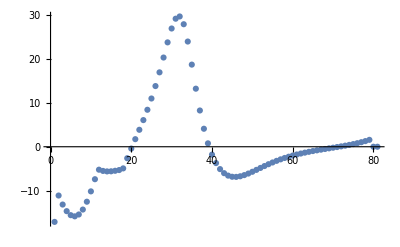

```mathematica
controldat = Import["trajoptdatu.csv"];
ListPlot[Flatten[controldat], PlotRange->All]
```

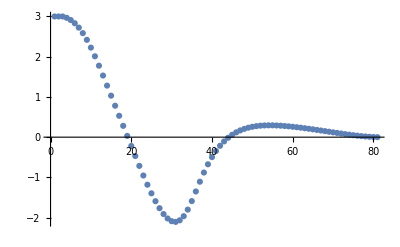

```mathematica
ListPlot[qcontroldattrajopt[[;;, 1]], PlotRange->All]
```

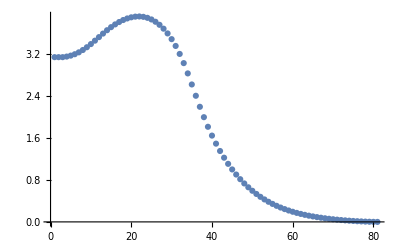

```mathematica
ListPlot[qcontroldattrajopt[[;;, 2]], PlotRange->All]
```

```mathematica
(*So these are the soltions obtained at the collocation points of the transcription. Now we need to interpolate these solutions*)
```

```mathematica
(*Interpolation*)
```

Control input was assumed to be linear in nature and hence will be its interpolation as,
β = (-1/h) * (u(k) - u(k-1))
u(t) = u(k) + δ(k) β
where δk = t - tk

Where as since the dynamics was assumed to be linear, the state approximation would be quadratic
γk = -1/(2*h) * (f(k) - f(k+1))
x(t) = x(k) + δk * f(k) + δk^2 *γk

```mathematica
(*Verifying the solution accuracy*)
```

```mathematica
(*We need to interpolate and then use the original dynamics equations to find the difference between these and plot them. Also After we get to this stage, we should check for the h-convergence.*)
```